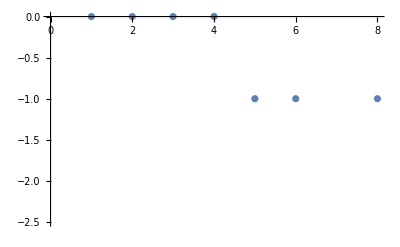

```mathematica
(*Exercises 1*)

list1 = {};
y = 10^3;
f[x_,y_] = (((x+y)^2)- 2 x y - y^2)/(x^2);
expected = 1;
For[i = 1, i ≤ 8, ++i,
e = f[(10.0^(-i)),y] - expected;
AppendTo[list1,e];
];
ListPlot[list1]
```

```mathematica
(*Exercise 2*)
```

```mathematica
list2 = {};
y = 10^3;
g[x_,y_] = (((x+y)^2)/x^2)- (2 x y/(x^2)) - (y^2)/(x^2);
expected = 1;
For[i = 1, i ≤ 8, ++i,
e = f[(10.0^(-i)),y] - expected;
AppendTo[list2,e];
];
ListPlot[list2]
```

```mathematica
(*The results appear to be the same. This occurs because g[x,10^3] = f[x,10^3]*) 

(*Exercise 3*)
```

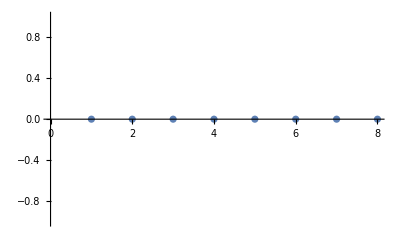

```mathematica
list3 = {};
y = 10^3;
f[x_,y_] = (((x+y)^2)- 2 x y - y^2)/(x^2);
expected = 1;
For[i = 1, i ≤ 8, ++i,
e = f[(10^(-i)),y] - expected;
AppendTo[list3,e];
];
ListPlot[list3]
```

```mathematica
Head[10]
Head[10.0]
```

Integer

Real

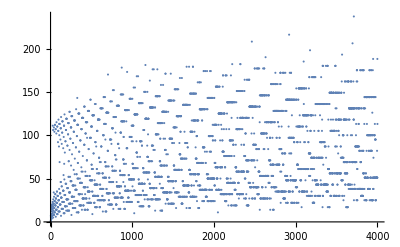

```mathematica
(*The results from Problem 3 are different because when we use 10.0, Mathematica reads it as a real number, while when we use 10, Mathematica reads it as an integer*)

(*Collatz Conjecture*)

list4 = {};
For[i = 1, i ≤ 4000, ++i,
n = i;
counter = 0;
While[n>1,
If[Mod[n,2] == 0,
n = n/2,
n = 3 n + 1];
counter = counter +1;
];
AppendTo[list4, counter] 
];

ListPlot[list4]
```

```mathematica
(*Midpoint Method*) 

(*Exercise 1*)
f[x_] = x^3;
x1= -.3;
x2 = .5;
testroot = x1;
testvalue = 10^-5;
While[Abs[f[testroot]] > testvalue,
testroot = (x1 + x2)/2;
If[f[testroot]*f[x1] ≥ 0,
x1 = testroot,
x2 = testroot
];
];
Print[testroot]
```

6.93889×10^-18

```mathematica
(*Exercise 2*)
```

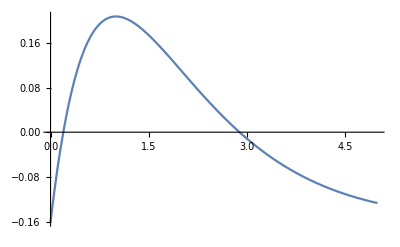

f(x) = 0 at 23673/8192

```mathematica
f[x_] = x*E^(-x)-0.16064;
Plot[f[x],{x,0,5}]
x3= 2;
x4 = 3;
testroot = x3;
testvalue = 10^-5;
While[Abs[f[testroot]] > testvalue,
testroot = (x3 + x4)/2;
If[f[testroot]*f[x3] ≥ 0,
x3 = testroot,
x4 = testroot
];
];
Print["f(x) = 0 at ",testroot]
```

```mathematica
f[x_] = x*E^(-x)-0.16064;
x3= 2;
x4 = 3;
testroot = x3;
testvalue = 10^-2;
While[Abs[f[testroot]] > testvalue,
testroot = (x3 + x4)/2;
If[f[testroot]*f[x3] ≥ 0,
x3 = testroot,
x4 = testroot
];
];
Print["f(x) = 0 at ",testroot]
```

f(x) = 0 at 23/8

```mathematica
relativeError = ((23673/8192)-(23/8))/(23673/8192);
N[relativeError, 10]
```

0.005111308241

```mathematica
(*Newton's Method*)
```

```mathematica
f[x_] = x^2;
g[x_] = D[f[x],x];
interlmt = 10000;
intercount = 0 ;
x5 = 0.2;
While[f[x]> 10^(-5) && intercount < interlmt,
x = x5 - f[x5]/g[x5];
intercount = intercount + 1
];
Print[intercount]
```

0

```mathematica
(*Not really sure how to do this one*)
```